# Friday 28th HW

### 4.5.12.c

```mathematica
f[z_]:= (√z-1)/(z-1)
ComplexPlot3D[f[z],{z,2}]
Series[f[z],{z,1,4}]
```

-Graphics3D-

1/2-(z-1)/8+1/16 (z-1)^2-5/128 (z-1)^3+7/256 (z-1)^4-(21 (z-1)^5)/1024+(33 (z-1)^6)/2048+O[z-1]^7

### 4.5.13.b

f1[z]=f2[z] for z≠0.

```mathematica
f1[z_]:= 1/((1-1/z^2)^2)
f2[z_]:= z^4/((z^2-1)^2)
TabView[{
"f1"->ComplexPlot3D[f1[z],{z,2}],
"f2"->ComplexPlot3D[f2[z],{z,2}]
}]
```

12

Depending on your tastes.  If you liked calculus II you can do partial fractions.

```mathematica
Apart[z^4/((z^2-1)^2)]
```

1+1/(4 (-1+z)^2)+3/(4 (-1+z))+1/(4 (1+z)^2)-3/(4 (1+z))

Alternatively f has a pole of order 2 at z=1.  Our “short-cut” trick says to 
multiply by (z-1)^2 to get rid of the negative powers and compute the Taylor Series of 
	g(z)=(z-1)^2 f(z)=a_0+a_1(z-1)+(a_2(z-1))^2+…
with  
	a_0 | = | lim_(z->1) g(z)
a_1 | = | lim_(z->1) g'(z)
a_2 | = | lim_(z->1) (g''(z))/(2!)
  | ⋮ |  
Dividing through by (z-1)^2 gives
	f(z)=a_0/(z-1)^2+a_1(z-1)/(z-1)^2+(a_2(z-1))^2/(z-1)^2+…

```mathematica
g[z_]:=(z-1)^2 f2[z]
Limit[g[z],z->1]
Limit[g'[z],z->1]
```

1/4

3/4

```mathematica
Residue[f2[z],{z,1}]
```

3/4

### 4.5.16

They ask us to look at a function with z complex and t a real parameter.  The first thing I would do is plot the thing! I can see the essential singularity at z=0!  Nothing else is going to cause any problems.

```mathematica
f[z_,t_]:= ⅇ^(t(z-1/z)/2)
t0=2.1;
ComplexPlot3D[f[z,t0],{z,1},PlotPoints->50,PlotLabel->t0]
```

-Graphics3D-

We know the TS expansion for ⅇ^z=∑_(k=0)^∞ z^k/(k!) so we can generate the Laurent Series for f 
	f=ⅇ^(t(z-1/z)/2)=ⅇ^((t z)/2).ⅇ^(-t/(2z))=∑_(k=0)^∞ ((t z)/2)^k/(k!)∑_(k=0)^∞ (-t/(2z))^k/(k!)=∑_(k=-∞)^∞ J_n(t)z^n
Your book is telling you that the coefficients which depend on t of the (one and only) Laurent Series define things called Bessel functions that are written J_n(t)

{BesselJ[0,t],BesselJ[1,t],BesselJ[2,t],BesselJ[3,t],BesselJ[4,t],BesselJ[5,t],BesselJ[6,t],BesselJ[7,t]}

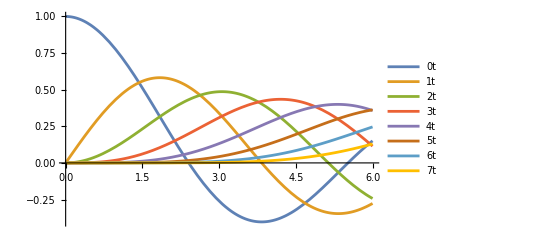

```mathematica
BFuns=Table[BesselJ[n,t],{n,0,7,1}]
Plot[BFuns ,{t,0,6},PlotLegends->"Expressions"]
```

They are asking you to show that the coefficients (i.e the Bessel functions) satisfy an ODE.  Some of you will have seen Bessel functions in ODE/PDE courses 
	https://en.wikipedia.org/wiki/Bessel_function
where they defined the Bessel J functions as the solutions of an ODE without telling you how to compute anything. What this HW is doing is looking at a “generating function” 
	https://en.wikipedia.org/wiki/Generating_function	
definition of the Bessel functions.  This “generating function” is a vaguely computable definition that defines J_0,J_1,… all at the same time.  It is reasonably easy to see that this definition automatically satisfies the ODE they gave you in the DE course.

```mathematica
Clear[TS,n,z]
TS[n_][z_]:=Sum[z^k/(k!),{k,0,n}]
TableForm[Table[
TS[n][t z/2]TS[n][- t/(2z)],{n,2,5}
]]
```

(1+t^2/(8 z^2)-t/(2 z)) (1+(t z)/2+(t^2 z^2)/8)
(1-t^3/(48 z^3)+t^2/(8 z^2)-t/(2 z)) (1+(t z)/2+(t^2 z^2)/8+(t^3 z^3)/48)
(1+t^4/(384 z^4)-t^3/(48 z^3)+t^2/(8 z^2)-t/(2 z)) (1+(t z)/2+(t^2 z^2)/8+(t^3 z^3)/48+(t^4 z^4)/384)
(1-t^5/(3840 z^5)+t^4/(384 z^4)-t^3/(48 z^3)+t^2/(8 z^2)-t/(2 z)) (1+(t z)/2+(t^2 z^2)/8+(t^3 z^3)/48+(t^4 z^4)/384+(t^5 z^5)/3840)